# 1D mean first passage time

Wikipedia has for the distribution of first passage times

```mathematica
fptpdf=(Δx/(Sqrt[4 Pi DD t^3]))Exp[-Δx^2/(4 DD t)]
```

(ⅇ^(-Δx^2/(4 DD t)) Δx)/(2 √π √(DD t^3))

```mathematica
DDorganelle=Quantity["BoltzmannConstant"]*Quantity[300,"Kelvins"]/((*6 Pi Quantity[.05,"Poise"]*)500* ChemicalData["Water","Viscosity"] Quantity[250,"Nanometers"])//UnitConvert
```

4.×10^-14 m^2/s

```mathematica
DDorganelle=Quantity[5*^-11,"Centimeters"^2/"Seconds"]//UnitConvert
```

1/200000000000000 m^2/s

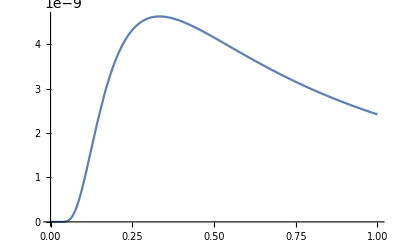

```mathematica
Plot[fptpdf/.{Δx->.001,DD->QuantityMagnitude[DDorganelle]},{t,0,100000000},PlotRange->All]
```

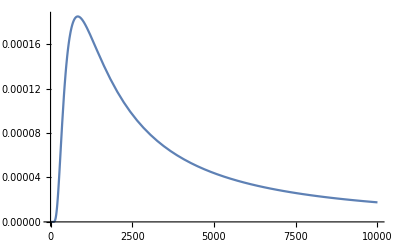

```mathematica
Plot[fptpdf/.{Δx->5*^-6,DD->QuantityMagnitude[DDorganelle]},{t,0,10000},PlotRange->All]
```

```mathematica
peak=Solve[D[fptpdf,t]==0]
```

{{Δx→0},{Δx→-√6 √DD √t},{Δx→√6 √DD √t}}

```mathematica
characteristicTime=Solve[Δx==(Δx/.peak[[3]]),t]
```

{{t→Δx^2/(6 DD)}}

```mathematica
characteristicTime/.{DD->QuantityMagnitude[DDorganelle],Δx->.001}
```

{{t→3.33333×10^7}}

```mathematica
UnitConvert[Quantity[t/.%[[1,1]],"Seconds"],"Days"]
```

385.802 days

```mathematica
characteristicTime/.{DD->QuantityMagnitude[DDorganelle],Δx->10*^-6}
```

{{t→10000/3}}

```mathematica
UnitConvert[Quantity[t/.%[[1,1]],"Seconds"],"Minutes"]//N
```

55.5556 min